# Generating Training Data

## Tyson Jones tyson.jones@monash.edu July 2017

```mathematica
Clear["Global`*"]
PacletDirectoryAdd[NotebookDirectory[]];
<< PlotFunctions`
<< EigenFunctions`
```

## potential ceiling

### theoretical discussion

This is all rubbish. The non-dimensional Schrodinger equation has already scaled space and time by a parameter of the potential (natural oscillator units). There is a scale invariance already built-in, even on a fixed domain.

Scaling space by α in the Schrodinger equation, and evaluating the derivative by the chain rule

```mathematica
Ε ϕ[x] == -1/2 ϕ''[x] + V[x] ϕ[x] /.   { x -> α x,  ϕ''[x]-> 1/α^2 ϕ''[α x] }
```

Ε ϕ[x α]==V[x α] ϕ[x α]-ϕ''[x α]/(2 α^2)

reveals a resulting squared coefficient in energy and potential.

```mathematica
Simplify[%, Assumptions-> {α ≠ 0}]
```

2 α^2 (Ε-V[x α]) ϕ[x α]+ϕ''[x α]==0

Though this does imply a quadratic scaling in energy, it does not in potential, which depends on position in general. For a constant system (V = 0; a free particle of a particle in an infinite potential well) it implies E scales with V, but for quadratic systems implies a quadratic scaling.

It’s therefore not generally possible to, given some scaling in the potential, a priori know the resulting scalings in energy and position of the eigenfunctions. This adds difficulty to choosing a ceiling potential value when generating training machine-learning training data.

In one limit, say V=constant, there is no functional scaling of potential with space. Scaling potential therefore linearly scales the energy, and shrinks space by the root, of the eigenfunctions. Horizontal shrinking is slower than vertical growth. E.g. the particle in an infinite square potential well has an energy E ∝ 1/L^2. Shrinking the domain should give an square increase in energy, as the energy formula corroborates.

Any polynomial positional dependence in the potential (e.g. V[x]  ∝ x^p for some p > 0) will see α^2 V[x α]  ∝ α^(2 + p) x^p and mean a growth in the potential scaling accompanies a smaller (relative to a scaled constant potential) shrinking in the x axis. Super-polynomial functions see a smaller horizontal scale change still. Non-differentiable potentials can have infinite polynomial expansions, and see no horizontal scaling from vertical.
Horizontal shrinking can cause great expanding of the axis, prompting truncated by the finite (static) numerical domain; reduction of the potential can thus drastically change the form of the eigenfunctions.

Also, energy eigenvalues can generally be greatly affected by the scaling of V; eigenfunctions can reshuffle haphazardly due to scaling.

### empirical demonstration

```mathematica
ShowSpectrum[ 
	1 UnitStep[-(#+2)] + 1 UnitStep[#-2] - 1 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/4 &)
]

ShowSpectrum[ 
	1000 UnitStep[-(#+2)] + 1000 UnitStep[#-2] - 1000 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/1000 &)
]
```

We observe scaling the potential can drastically altar the functional form of the lowest eigenfunctions.

```mathematica
ShowSpectrum[ 
	x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30&)
]

ShowSpectrum[ 
	10 x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30&)
]
```

Even mere horizontal scaling is significant on a fixed domain.

```mathematica
ShowSpectrum[ 
	-x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30 + 1&)
]

ShowSpectrum[ 
	-20 x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30 + 1&)
]
```

Finite precision of the discretised grid presents an upper bound to potential magnitude, above which smoothness is long forgone and Gibbs phenomena may appear.

```mathematica
ShowSpectrum[ 
	100/(.1x+.1),
	{x, 0, 1},
	PlotRange -> {0, 10},
	PotentialTransform -> (#/100&)
]
```

We can approximate reciprocal functions with polynomials.

### normalisation algorithm

#### procedure

Since translation of the potential is non-physical, we’ll arbitrarily fix the potential to fall between 0 and POTENTIALBOUND; this is global, and bounds all training potentials. POTENTIALBOUND will be very large (found experimentally below), so as to render maximum-potential regions as quasi-infinite, and the waveforms stable in form above it (beyond horizontal scaling).

We’ll randomly generate a potential form (see proceeding section) on the domain x ∈ [-5, 5] (wide enough to observe unity-coefficient polynomial growth) which is implicitly infinite at the grid boundaries, and normalise it to span [0, POTENTIALBOUND]. This will be the most extreme scaling of the potential of that form. We’ll also consider scalings of this potential between 0 and 1, distributed sensibly based on the experiment below. This should provide discovery of the distinct waveforms (beyond scaling) possible of the eigenbasis of each potential specification. We note our fixed grid size (and infinite potential well envelope) means this “scaling” isn’t just a vertical scaling of potential; it’s a subtle geometric change with possibly complicated effects on the energy eigenvalues.

#### potential bound experiment

We found a higher rate of compression for lower order potentials; these will be the first to reach the horizontal compression limit. We’ll study the linear and quadratic potentials (corresponding to Airy and Hermite functions). These are comfortably expressed with unity coefficients on the domain [-5, 5].

```mathematica
XLEFT = -5;
XRIGHT = 5;
```

```mathematica
ShowSpectrum[ 
	x,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,.8},
	PotentialTransform -> (#/2&)
]

ShowSpectrum[ 
	x^2,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,1},
	PotentialTransform -> (#/2&)
]
```

These functions become erroneously spiky (with default NumberOfPoints on x ∈ [-5, 5]) before coeff ~ 10^2, or potential maxima of 10^2 5^2 = 2500

```mathematica
UPPERBOUND = 10^2 5^2;
```

```mathematica
ShowSpectrum[ 
	10^2 x,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,.8},
	PotentialTransform -> (#/2&)
]

ShowSpectrum[ 
	10^2 x^2,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,1},
	PotentialTransform -> (#/2&)
]
```

```mathematica
adjustPotential[potential_, x___] :=
	Module[
		{grid, potentialList, minV, maxV},
			
		{grid, potentialList} = Discretise[potential, {x, XLEFT, XRIGHT}, NumberOfPoints -> 200];
		maxV = Max[potentialList];
		minV = Min[potentialList];
		N[(potentialList - minV)/(maxV - minV) UPPERBOUND]
	]
```

#### potential scaling distribution experiment

What distribution of scales should we use?

```mathematica
Manipulate[
	ShowSpectrum[
		c adjustPotential[ 1 UnitStep[-(#+2)] + 1 UnitStep[#-2] - 1 UnitStep[#-3] &],
		{XLEFT, XRIGHT},
		PlotRange -> {0, 4}
	],
	{c, 0, 1}
]
```

```mathematica
getPotentialScalings[potential_, x___] :=
	With[
		{
			fullPotential = adjustPotential[potential, x],
			scalings = Table[10^n, {n, -4, 0}] // N
		},
		Table[scalings[[n]] fullPotential, {n, Length[scalings]}]
	]
```

```mathematica
With[
	{scaledVs = getPotentialScalings[ x^3, x]},
	Manipulate[
		ShowSpectrum[
			scaledVs[[n]],
			{XLEFT, XRIGHT},
			PlotRange -> {0, 4}
		],
		{n,1, Length[scaledVs], 1}
	]
]
```

Our scaling shows good variation for a given potential form, though looks linear for most forms in the large scaling, yielding Airy functions.

```mathematica
With[
	{scaledVs = getPotentialScalings[1 UnitStep[-(#+2)] + 1 UnitStep[#-2] - 1 UnitStep[#-3] &]},
	Manipulate[
		ShowSpectrum[
			scaledVs[[n]],
			{XLEFT, XRIGHT},
			PlotRange -> {0, 4}
		],
		{n,1, Length[scaledVs], 1}
	]
]
```

This may be undone by step potentials. Since step functions don’t grow in x, their amplitudes should be able to appear of similar size to the max value of the greatest order polynomial in the potential. E.g. [-1, 1] XRIGHT^p UnitStep[x + [-5, 5]]

```mathematica
With[
	{scaledVs = getPotentialScalings[ .1 x^3 + .4 x^6 - .7 x^7 + .2 x^4 + 0.3 XRIGHT^7  UnitStep[x], x]},
	Manipulate[
		ShowSpectrum[
			scaledVs[[n]],
			{XLEFT, XRIGHT},
			PlotRange -> {0, 4}
		],
		{n,1, Length[scaledVs], 1}
	]
]
```

## potential forms

Our aim to produce a potential with form

V(x) |_(XLEFT < x < XRIGHT) = Σ_i^p c_i|_Pr_i x^i +  (Σ^s)_j d_j|_U XRIGHT^p Step(x + XRIGHT t_j|_U)

where the step amplitudes and translations d_j, t_j ∈ [-1, 1] are uniformly distributed (on U) and the polynomial coefficients c_i ∈ [-1, 1] follow some degree-dependent distribution Pr_i still to be decided. Integers p and s are the polynomial degree and number of present step potentials respectively, and are fixed a-priori.

We now decide p, s and Pr_i.

### coefficients, terms and translation distributions

For a grid x ∈ [XLEFT = -5, XRIGHT=5] with potentials bounded by [0, UPPERBOUND = 2500], we hypothesised generating polynomials of degree 1, 2, ..., p with c_i ∈ [-1, 1] coefficients superposed with step potentials of amplitude [-1, 1]  XRIGHT^p and translations dx = [XLEFT, XRIGHT] will generate many interesting potentials.

#### choosing a degree (p) and coefficient distribution (Pr_i)

We must now choose the polynomial order of the potential, and what probability distribution each coefficient should follow. Let’s first test uniform coefficients.

```mathematica
getUniformRandomPolynomial[x_:x, order_:5] :=
	Total[Table[RandomReal[{-1,1}] x^n, {n, order}]]
```

```mathematica
Manipulate[
(Plot[# /. x -> r, {r, XLEFT, XRIGHT}]&) /@ Table[getUniformRandomPolynomial[x, p], {dummyvar, 9}],
{p, 1, 10, 1},
ContinuousAction->False
]
```

These plots look largely the same; a uniform distribution for each coefficient (Pr_i = U  ∀ i) sees the greatest degree power dominate the large-scale potential behaviour.
We’ll need some family of distributions where the expectation of the absolute value of the outcome decreases with increasing i.
Since higher terms dominate polynomially, we should use a distribution with polynomial scaling on the parameter.

```mathematica
getInverseRandomPolynomial[x_:x, order_:6] :=
	Total[Table[ RandomReal[{-1,1}]n  XRIGHT^-n x^n, {n, order}]]
```

Note forcing the total degree positive will not force positive limiting behaviour, and setting the greatest-degree coefficient large will break all behaviour (not just limiting)

```mathematica
Manipulate[
(Plot[
	# /. x -> r,
	 {r, c XLEFT, c XRIGHT},
	PlotRange->All
]&) /@ Table[getInverseRandomPolynomial[x, p], {numofplotsdummyvar, 9}],
{{p,100}, 1, 100, 1},
{{c, 0.65}, 0.01, 1},
ContinuousAction->False
]
```

These plots have desirable distinct landscape on inner regions ([-3, 3]), and good rapid growth outside  (making our training data “less particle-in-a-boxy”). Negative boundary behaviour will need to be solved without polynomials. Notice the local range of the function doesn’t grow with the upper degree! We can work in quasi-linear regimes!

We decide on degree p=100 and distribution 
 c_i|_Pr_i =  c2_i|_U i  XRIGHT^-i

```mathematica
getRandomPolynomial[x_] :=
	getInverseRandomPolynomial[x, 100]
```

#### choosing number of steps (s)

Having chosen a drastic degree-dependence in the coefficients of the polynomials, we’ll need to decide a new maximum amplitude for our step functions. The range of our poly’s in [-5, 5] is approx linear in the domain; we’ll simply choose linear (with XRIGHT) amplitudes!

We’ll merely experiment on a sufficient number of step terms in the potential; it may also be random.

```mathematica
getRandomStepsFixedNum[x_:x, s_:5] :=
	Total[Table[
		XRIGHT RandomReal[{-1, 1}] UnitStep[x + XRIGHT RandomReal[{-1, 1}]],
		{dummyvar, s}
	]]
```

```mathematica
Manipulate[
	With[
		{V = getRandomStepsFixedNum[r, s]},
		Plot[
		 V /. r -> x,
		{x, XLEFT, XRIGHT},
		Exclusions-> None
		]
	],
	{s, 1, 20, 1}
]
```

A number is better decided by observing the total deformation to the potential.

```mathematica
Manipulate[
	With[
		{V = getRandomStepsFixedNum[r, s] + getRandomPolynomial[r]},
		Plot[
		 V /. r -> x,
		{x, XLEFT, XRIGHT},
		Exclusions-> None
		]
	],
	{s, 1, 20, 1}
]
```

A random number in [0, 5] seems ideal

```mathematica
getRandomSteps[x_] :=
	 getRandomStepsFixedNum[x, RandomInteger[{0,5}]]
```

### sampling and smoothing

We’ve outlined parameters and distributions to create

V(x) |_(XLEFT < x < XRIGHT) = Σ_i^100 c_i|_U[-1,1] i  XRIGHT^-i  x^i +  (Σ^U[0,5])_j d_j|_U[-1.1] XRIGHT Step(x + XRIGHT t_j|_U[-1,1])

Note that the local and boundary behaviours are very different.

```mathematica
Manipulate[
	With[
		{V =Function @@ {getRandomSteps[#] + getRandomPolynomial[#]}},
		Plot[
		V[x],{x, -5, 5}, Exclusions-> None,
		PlotRange->plotrange
		]
	],
	{plotrange, {Automatic, All}}
]
```

We’ll simply horizontally scale the function to avoid these “boundary plummets”.
[-4.5, 4.5] → [-5, 5] is a scale factor of 4.5/5

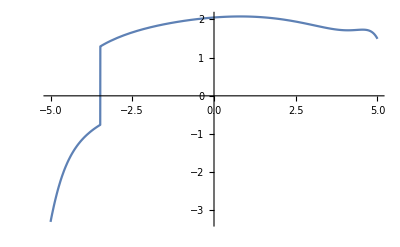

```mathematica
With[
		{V = getRandomPotentialFunction[]},
		Plot[
		V[x 4.5/5],{x, -5, 5}, Exclusions-> None,
		PlotRange->All
		]
	]
```

```mathematica
getRandomPotential[x_] :=
	getRandomSteps[x 4.5/5] + getRandomPolynomial[x 4.5/5]
```

```mathematica
getRandomPotentialFunction[] :=
	Function @@ {getRandomPotential[#]}
```

Finally, our potential is scaled between [0, UPPERBOUND=2500]

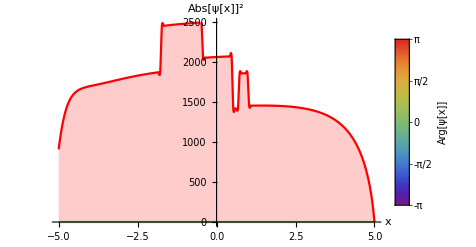

```mathematica
With[
	{V = adjustPotential[getRandomPotentialFunction[]]},
	PlotWavefunction[
		0, {XLEFT, XRIGHT},
		Potential -> V,
		PlotRange -> {0, UPPERBOUND}
	]
]
```

and a distribution of scalings of UPPERBOUND are used for finding solutions.

```mathematica
With[
	{VScalings = getPotentialScalings[getRandomPotentialFunction[]]},
	Manipulate[
		PlotWavefunction[
			0, {XLEFT, XRIGHT},
			Potential -> VScalings[[s]],
			PlotRange -> {0,UPPERBOUND}
		],
		{s, 1, Length[VScalings],1}
	]
]
```

We finally remark that we’re still making a very particular sampling of potentials; relative variation of our potentials is very small. For example, there’s no simulation of a quadratic potential (which keeps growing boundaries).

## Formatting Solutions

```mathematica
With[
	{VScalings = getPotentialScalings[getRandomPotentialFunction[]]},
	Manipulate[
		ShowSpectrum[ 
			VScalings[[scaling]], {XLEFT, XRIGHT},
			PotentialTransform -> (#/10 &),
			PlotRange -> All
		],
		{scaling, 1, Length[VScalings], 1}
	]
]
```

```mathematica
NetModel["Inception V1 Trained on ImageNet Competition Data"]
```

NetChain[]